# Quantum dot

In this notebook we consider one particular example of nc rational functions: the one that appears in the paper of Beenakker

```mathematica
SetDirectory[NotebookDirectory[]];
```

Add the folder(s) containing the current package as well as NC package to $Path

```mathematica
AppendTo[$Path,"/Users/yumish/Dropbox/a_recherche/mathematica_all/mathematica_packages/"];
<<NC` (*load NCAlgebra*)
<<NCAlgebra`
<<PolynomialsOfRandomMatrices`
```

NC::Directory: You are using the version of NCAlgebra which is found in: "/Users/yumish/Library/CloudStorage/Dropbox/a_recherche/mathematica_all/mathematica_packages/NC/".

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

```mathematica
DoSplot[N[LLP/.En->-1],{-.5,1.5},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.5,1.5},{0,100}},Ticks->Automatic,PlotLegends->Automatic]
```

```mathematica
Options[DoSplot]=Join[{SolutionAccuracy->0.001,Iterations->5000,ImaginaryPart->0.001,GridNumber->1000,Rescaling->1},Options[Plot]];
DoSplot[LLinearization_,Interval_,opts:OptionsPattern[]]:=Block[{VVariableList,LL0,LL,JJ,SSOperator,MM},

MM=IterativelySolveMDEonInterval2[LLinearization,z ,Interval[[1]],Interval[[2]],OptionValue[ImaginaryPart],OptionValue[GridNumber],OptionValue[Iterations],OptionValue[SolutionAccuracy]];

Return[ListLinePlot[
Table[{MM[[i,1]],Im[MM[[i,2]][[1,1]]]/Pi*OptionValue[Rescaling]},{i,Length[MM]}],FilterRules[{opts},Options[Plot]],PlotRange->{0,1.02 Max[Table[Im[MM[[i,2]][[1,1]]]/Pi,{i,Length[MM]}]]},Ticks->Automatic,PlotLegends->Automatic,ImageSize->270,PlotStyle->{Blue,Thick},Filling->Bottom]];
];
```

### Computing Fano factor

*Function FanoFactor[evlist]

```mathematica
FanoFactor[evlist_]:=Block[{list01},
(*list01=Select[evlist,(#>0 && #<1)&];*)
list01=evlist;
Return[Sum[list01[[i]]*(1-list01[[i]]),{i,Length[list01]}]/Total[list01]];
];
```

## Linearization (run)

We define the semicircular elements x, s, t, u, v, so that y_1=(s+i t)/√2, y_2=(u+i v)/√2. 
The initial linearization

```mathematica
Clear[En];
LL={{-z,0,0,0,0,(u-ⅈ*v)/Sqrt[2],0,0},{0,0,0,0,(s+ⅈ*t)/Sqrt[2],En-x,(s+ⅈ*t)/Sqrt[2],(u+ⅈ*v)/Sqrt[2]},{0,0,0,0,0,(s-ⅈ*t)/Sqrt[2],ⅈ/Pi,0},{0,0,0,0,0,(u-ⅈ*v)/Sqrt[2],0,ⅈ/Pi},{0,(s-ⅈ*t)/Sqrt[2],0,0,-1/(4*Pi^2),0,0,0},{(u+ⅈ*v)/Sqrt[2],En-x,(s+ⅈ*t)/Sqrt[2],(u+ⅈ*v)/Sqrt[2],0,0,0,0},{0,(s-ⅈ*t)/Sqrt[2],-ⅈ/Pi,0,0,0,0,0},{0,(u-ⅈ*v)/Sqrt[2],0,-ⅈ/Pi,0,0,0,0}};
MatrixForm@LL
```

(-z | 0 | 0 | 0 | 0 | (u-ⅈ v)/(√2) | 0 | 0
0 | 0 | 0 | 0 | (s+ⅈ t)/(√2) | En-x | (s+ⅈ t)/(√2) | (u+ⅈ v)/(√2)
0 | 0 | 0 | 0 | 0 | (s-ⅈ t)/(√2) | ⅈ/π | 0
0 | 0 | 0 | 0 | 0 | (u-ⅈ v)/(√2) | 0 | ⅈ/π
0 | (s-ⅈ t)/(√2) | 0 | 0 | -1/(4 π^2) | 0 | 0 | 0
(u+ⅈ v)/(√2) | En-x | (s+ⅈ t)/(√2) | (u+ⅈ v)/(√2) | 0 | 0 | 0 | 0
0 | (s-ⅈ t)/(√2) | -ⅈ/π | 0 | 0 | 0 | 0 | 0
0 | (u-ⅈ v)/(√2) | 0 | -ⅈ/π | 0 | 0 | 0 | 0)

Now we obtain the linearization leading to the block structure

```mathematica
P23=SparseArray[{{1,1}->1,{2,3}->1,{3,2}->1,{4,4}->1,{5,5}->1,{6,6}->1,{7,7}->1,{8,8}->1}];
P28=SparseArray[{{1,1}->1,{2,8}->1,{3,3}->1,{4,4}->1,{5,5}->1,{6,6}->1,{7,7}->1,{8,2}->1}];
P67=SparseArray[{{1,1}->1,{2,2}->1,{3,3}->1,{4,4}->1,{5,5}->1,{6,7}->1,{7,6}->1,{8,8}->1}];
P34=SparseArray[{{1,1}->1,{2,2}->1,{3,4}->1,{4,3}->1,{5,5}->1,{6,6}->1,{7,7}->1,{8,8}->1}];
P78=SparseArray[{{1,1}->1,{2,2}->1,{3,3}->1,{4,4}->1,{5,5}->1,{6,6}->1,{7,8}->1,{8,7}->1}];
P47=SparseArray[{{1,1}->1,{2,2}->1,{3,3}->1,{4,7}->1,{5,5}->1,{6,6}->1,{7,4}->1,{8,8}->1}];
P25=SparseArray[{{1,1}->1,{2,5}->1,{3,3}->1,{4,4}->1,{5,2}->1,{6,6}->1,{7,7}->1,{8,8}->1}];P35=SparseArray[{{1,1}->1,{2,2}->1,{3,5}->1,{4,4}->1,{5,3}->1,{6,6}->1,{7,7}->1,{8,8}->1}];
P46=SparseArray[{{1,1}->1,{2,2}->1,{3,3}->1,{4,6}->1,{5,5}->1,{6,4}->1,{7,7}->1,{8,8}->1}];
LLP=P78.P23.P34.P67.P28.LL.P28.P67.P34.P23.P78;
LLP2=P46.P35.P25.P47.LL.P47.P25.P35.P46;
MatrixForm@LLP
MatrixForm@LLP2
```

(-z | 0 | 0 | 0 | 0 | 0 | 0 | (u-ⅈ v)/(√2)
0 | 0 | ⅈ/π | 0 | 0 | 0 | 0 | (u-ⅈ v)/(√2)
0 | -ⅈ/π | 0 | 0 | 0 | 0 | (u-ⅈ v)/(√2) | 0
0 | 0 | 0 | 0 | 0 | ⅈ/π | 0 | (s-ⅈ t)/(√2)
0 | 0 | 0 | 0 | -1/(4 π^2) | 0 | (s-ⅈ t)/(√2) | 0
0 | 0 | 0 | -ⅈ/π | 0 | 0 | (s-ⅈ t)/(√2) | 0
0 | 0 | (u+ⅈ v)/(√2) | 0 | (s+ⅈ t)/(√2) | (s+ⅈ t)/(√2) | 0 | En-x
(u+ⅈ v)/(√2) | (u+ⅈ v)/(√2) | 0 | (s+ⅈ t)/(√2) | 0 | 0 | En-x | 0)

(-z | 0 | 0 | (u-ⅈ v)/(√2) | 0 | 0 | 0 | 0
0 | -1/(4 π^2) | (s-ⅈ t)/(√2) | 0 | 0 | 0 | 0 | 0
0 | (s+ⅈ t)/(√2) | 0 | En-x | 0 | (s+ⅈ t)/(√2) | 0 | (u+ⅈ v)/(√2)
(u+ⅈ v)/(√2) | 0 | En-x | 0 | (s+ⅈ t)/(√2) | 0 | (u+ⅈ v)/(√2) | 0
0 | 0 | 0 | (s-ⅈ t)/(√2) | 0 | ⅈ/π | 0 | 0
0 | 0 | (s-ⅈ t)/(√2) | 0 | -ⅈ/π | 0 | 0 | 0
0 | 0 | 0 | (u-ⅈ v)/(√2) | 0 | 0 | 0 | ⅈ/π
0 | 0 | (u-ⅈ v)/(√2) | 0 | 0 | 0 | -ⅈ/π | 0)

## Superoperator Γ and related matrices (run)

### Definitions

```mathematica
Clear[En];
```

```mathematica
K=SparseArray[{{7,8}->-1,{8,7}->-1},{8,8}];MatrixForm@K
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
L1=SparseArray[{{7,5}->1,{7,6}->1,{8,4}->1},{8,8}];MatrixForm@L1
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
L2=SparseArray[{{7,3}->1,{8,1}->1,{8,2}->1},{8,8}];MatrixForm@L2
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
κ1=SparseArray[{{2,3}->ⅈ/Pi,{3,2}->-ⅈ/Pi},{3,3}];MatrixForm@κ1
```

(0 | 0 | 0
0 | 0 | ⅈ/π
0 | -ⅈ/π | 0)

```mathematica
κ2=SparseArray[{{1,3}->ⅈ/Pi,{3,1}->-ⅈ/Pi,{2,2}->-1/(4*Pi^2)},{3,3}];MatrixForm@κ2
```

(0 | 0 | ⅈ/π
0 | -1/(4 π^2) | 0
-ⅈ/π | 0 | 0)

```mathematica
κ3={{0,1},{1,0}};MatrixForm@κ3
```

(0 | 1
1 | 0)

```mathematica
κ4={{0,1,1},{1,0,0}};MatrixForm@κ4
```

(0 | 1 | 1
1 | 0 | 0)

```mathematica
κ5={{0,0,1},{1,1,0}};MatrixForm@κ5
```

(0 | 0 | 1
1 | 1 | 0)

```mathematica
K0={{0,0,0,0,0,0,0,0},{0,0,ⅈ/Pi,0,0,0,0,0},{0,-ⅈ/Pi,0,0,0,0,0,0},{0,0,0,0,0,ⅈ/Pi,0,0},{0,0,0,0,-1/(4*Pi^2),0,0,0},{0,0,0,-ⅈ/Pi,0,0,0,0},{0,0,0,0,0,0,0,En},{0,0,0,0,0,0,En,0}};MatrixForm@(K0/.En->1)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/π | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/π | 0 | 0
0 | 0 | 0 | 0 | -1/(4 π^2) | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Γ[R_]:=K.R.K+L1.R.ConjugateTranspose[L1]+ConjugateTranspose[L1].R.L1+L2.R.ConjugateTranspose[L2]+ConjugateTranspose[L2].R.L2;
```

## Numerical solution of the MDE

#### Plots of the DoS for different values of E

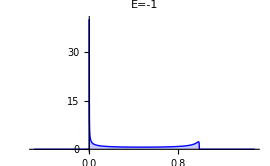
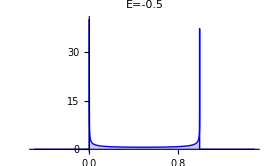
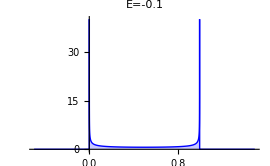
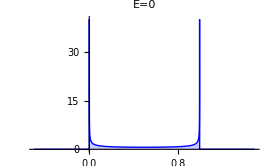
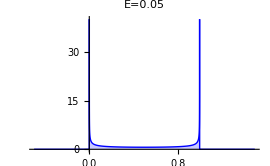
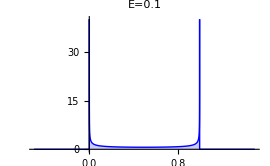
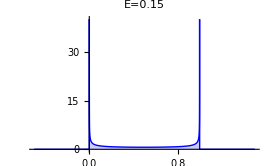
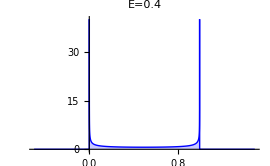

```mathematica
p={};EnList={-1,-0.5 ,-0.1,0, 0.05, 0.1,0.15,0.4,0.5,0.6,0.7,1,2,5};
Do[plotLabel="E="<>ToString[EnList[[ind]]];
p=Append[p,DoSplot[N[LLP/.En->EnList[[ind]]],{-.5,1.5},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.5,1.5},{0,40}},Ticks->Automatic,PlotLegends->Automatic,PlotLabel->Style[plotLabel,FontColor->Red]]] 
,{ind,Length[EnList]}];
Table[Table[p[[ind*2+j]],{j,2}],{ind,0,Length[EnList]/2 - 1}]
```

### Density of states around z=1 for En between 0.6 and 0.7 (critical values)

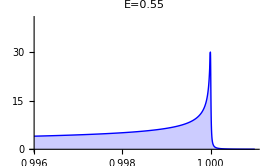
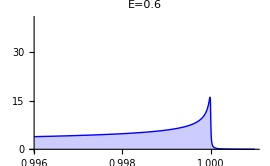
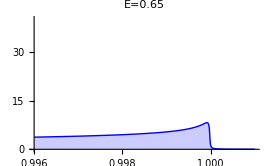
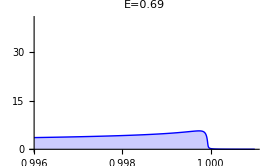
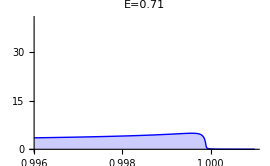
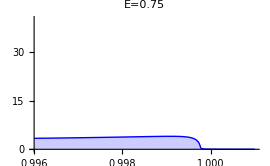
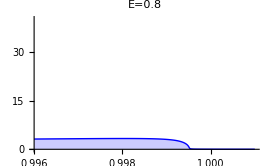
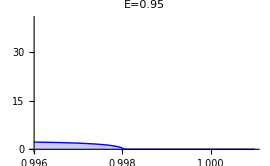

```mathematica
p={};EnList={0.55,0.6,0.65,0.69,0.71,0.75,0.8,0.95};
Do[plotLabel="E="<>ToString[EnList[[ind]]];
p=Append[p,DoSplot[N[LLP/.En->EnList[[ind]]],{.996,1.001},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{.996,1.001},{0,40}},Ticks->Automatic,PlotLegends->Automatic,PlotLabel->Style[plotLabel,FontColor->Red]]] 
,{ind,Length[EnList]}];
Table[Table[p[[ind*2+j]],{j,2}],{ind,0,Length[EnList]/2 - 1}]
```

## Compare the histogram for the simulated matrix and the DOS for the corresponding MDE (DEL)

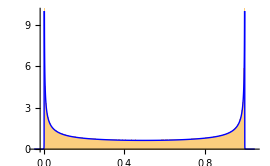
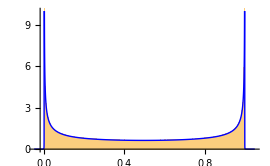
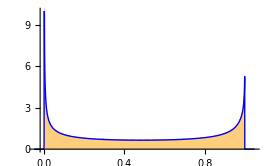
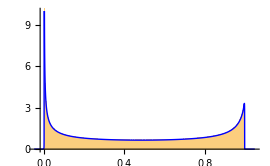
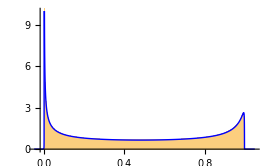
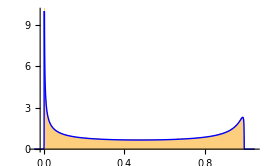

```mathematica
p={};EnList={-0.1,0.0,0.7,0.8,0.9,1.0};EnTextList={"_01","00","07","08","09","10"};
Do[fileName="./ev_40K_interval/Eigenvalues40Kat"<>EnTextList[[ind]]<>"a.wdx";
plotLabel="E="<>ToString[EnList[[ind]]];
ev=Import[fileName];
p=Append[p,Show[Histogram[Re[ev],500,"PDF"],DoSplot[N[LLP/.En->EnList[[ind]]],{-.05,1.05},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.5,1.5},{0,10}},Ticks->Automatic,PlotLegends->Automatic,Filling->None],PlotRange->{{-0.05,1.05},{0,10}},ImageSize-> 270]] 
,{ind,Length[EnList]}];
Table[Table[p[[ind*2+j]],{j,2}],{ind,0,Length[EnList]/2 - 1}]
```

## Fano Factor for different E=-0.1, 0, 0.1, 0.1, ..., 0.9, 1, 1.1 (matrix size N=40 000, computations performed on the IST server, loaded from the files)

```mathematica
EnList=Range[-0.1,1.0,0.1];EnTextList={"_01","00","01","02","03","04","05","06","07","08","09","10"};
Do[fileName="./ev_40K_interval/Eigenvalues40Kat"<>EnTextList[[ind]]<>"a.wdx";
ev=Import[fileName];
Print["Fano factor at E="<>ToString[EnList[[ind]]]<>": "<>ToString[FanoFactor[Re[ev]]]];
,{ind,Length[EnList]}];
```

Fano factor at E=-0.1: 0.249543

Fano factor at E=0.: 0.249237

Fano factor at E=0.1: 0.24955

Fano factor at E=0.2: 0.250428

Fano factor at E=0.3: 0.2519

Fano factor at E=0.4: 0.253912

Fano factor at E=0.5: 0.256423

Fano factor at E=0.6: 0.259419

Fano factor at E=0.7: 0.262821

Fano factor at E=0.8: 0.266585

Fano factor at E=0.9: 0.27066

Fano factor at E=1.: 0.274972

## Compare (roughly) the DOS and the arcsine distribution, globally and on some short intervals, near edges and inside the bulk

```mathematica
arcsineplot[aa_,bb_]:=ListLinePlot[Table[{aa+i*(bb-aa)/1000,1/(N[Pi]*Sqrt[(aa+i*(bb-aa)/1000)*(1-(aa+i*(bb-aa)/1000))])},{i,1,999}],PlotStyle->{Red,Thick,Dashed},PlotRange->Full];
```

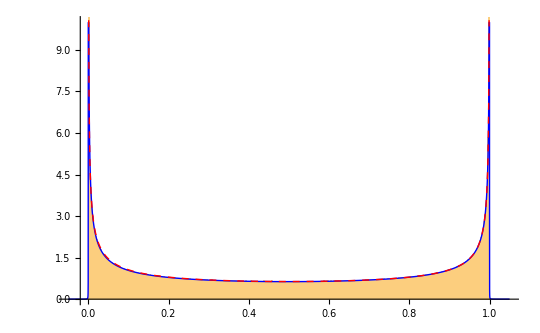

```mathematica
ev=Import["./ev_40K_interval/Eigenvalues40Kat_01a.wdx"];Show[Histogram[Re[ev],500,"PDF"],DoSplot[N[LLP/.En->-0.1],{-.05,1.05},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.5,1.5},{0,10}},Ticks->Automatic,PlotLegends->Automatic,Filling->None],arcsineplot[0,1],PlotRange->{{-0.05,1.05},{0,10}},ImageSize->540]
```

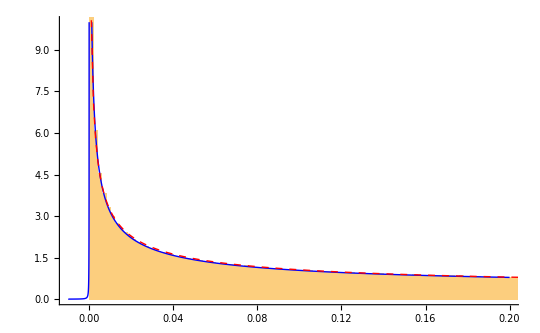

```mathematica
ev=Import["./ev_40K_interval/Eigenvalues40Kat_01a.wdx"];Show[Histogram[Re[ev],500,"PDF"],DoSplot[N[LLP/.En->-0.1],{-.01,0.2},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.01,0.2},{0,10}},Ticks->Automatic,PlotLegends->Automatic,Filling->None],arcsineplot[0,1],PlotRange->{{-0.01,0.2},{0,10}},ImageSize->540]
```

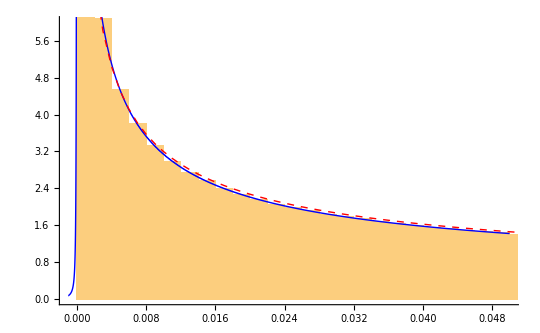

```mathematica
ev=Import["./ev_40K_interval/Eigenvalues40Kat_01a.wdx"];Show[Histogram[Re[ev],500,"PDF"],DoSplot[N[LLP/.En->-0.1],{-.001,0.05},SolutionAccuracy->0.0001,Iterations->50000,ImaginaryPart->0.00001,GridNumber->5000,PlotRange->{{-0.001,0.05},{0,10}},Ticks->Automatic,PlotLegends->Automatic,Filling->None],arcsineplot[0,1],PlotRange->{{-0.001,0.05},{0,6}},ImageSize->540]
```

## Plot the Fano factor as a function of parameter ϕ (load the values of the Fano factor computed on the IST server)

```mathematica
dataF={};
```

```mathematica
Do[fanophi=Import[StringTemplate["./fano_phi_50_9k/phi_`a`50_9k.wdx"][<|"a"->k|>]];
dataF=Join[dataF,{{fanophi[[1]],fanophi[[3]]}}];,{k,1,49}]
```

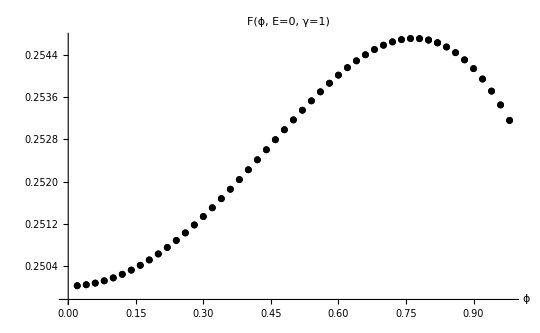

```mathematica
ListPlot[dataF,TicksStyle->{{FontSize->12,FontFamily->"Serif"},{FontSize->12,FontFamily->"Serif"}},AxesLabel->{"ϕ", None},LabelStyle->{FontSize->12,FontFamily->"Serif"},PlotLabel->"F(ϕ, E=0, γ=1)" ,PlotStyle->Black,ImageSize->540]
```